## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = False;
removeOutputFiles = False;

rxnName="TPI";
fitLabel="new_lma_1";
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)

(* user will need to change this path *)
pathMASSef = "/home/mrama/Desktop/MASSef/";
kineticDataFileName =  "kinetic_data_MASSef.csv";

mainFolder = "fit_TPI";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/home/mrama/Dropbox/MASSef/examples/TPI/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

{g3p,Null,Keq substrate}

{9.35,Keq value}

{g3p,Km or S05 substrate}

{0.00103,Km or S05 value}

{{{g3p,Null}},kcat substrates}

{9000,kcat value}

{2-phosphoglycolate,Inhibition or activation constant substrate}

{0.006,Inhibition or activation constant value}

(g3p^c⇌dhap^c)^TPI

;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p,Null | 9.35 | 8.8825
9.8175 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | 0.00103 | 0.00093
0.00113 |  | M | 7.6 | 25 | teoahcl | 0.1 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | Null | 27025.3 | 26523.8
27526.8 | 1/s | 7.6 | 37 | teoahcl | 0.1 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Ki | 2-phosphoglycolate | 0.006 | 0.0057
0.0063 |  | Competitive | dhap | Null | M | 7.6 | 25 | teoahcl | 0.1 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority (optional)

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1}(*{10}*);
s05Priorities = Null;
kcatPriorities = {1}(*{0.0001}*);
inhibitionPriorities={0};
activationPriorities = Null;
otherParamsPriorities =Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(g3p^c⇌dhap^c)^TPI

;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p,Null | 9.35 | 8.8825
9.8175 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | 0.00103 | 0.00093
0.00113 |  | M | 7.6 | 25 | teoahcl | 0.1 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | Null | 27025.3 | 26523.8
27526.8 | 1/s | 7.6 | 37 | teoahcl | 0.1 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### mechanism

```mathematica
catalyticBranch={"E_TPI[c] + g3p[c] <=> E_TPI[c]&g3p",
				"E_TPI[c]&g3p <=> E_TPI[c]&dhap",
				"E_TPI[c]&dhap <=> E_TPI[c] + dhap[c]"};

enzymeModelOrig=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModelOrig["Reactions"]
```

{((TPI^c)_^+g3p^c⇌(TPI^c&g3p^c)_^)^TPI1,((TPI^c&dhap^c)_^⇌(TPI^c)_^+dhap^c)^TPI2,((TPI^c&g3p^c)_^⇌(TPI^c&dhap^c)_^)^TPI3}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1=enzymeModelOrig["Reactions"];
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
Get["MASSef`"];
```

```mathematica
deleteDirectoryContents[inputPath];
```

```mathematica
MWCFlag=False;
nActiveSites=1;
assumedSaturatingConc = 1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModelOrig, rxn, rxnName, inputPath, {},{}, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites, assumedSaturatingConc];
```

{g3p^c→0}

{dhap^c→0}

{g3p^c→1}

{dhap^c→1}

Added inhibition reactions:

{}

Loading flux equation...

Loading absolute rate forward equation...

Loading absolute rate reverse equation...

Loading relative rate forward equation...

Loading relative rate reverse equation...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

```mathematica
rxn
```

(g3p^c⇌dhap^c)^TPI

```mathematica
enzymeModel["Reactions"]
```

{((TPI^c)_^+g3p^c⇌(TPI^c&g3p^c)_^)^TPI1,((TPI^c&dhap^c)_^⇌(TPI^c)_^+dhap^c)^TPI2,((TPI^c&g3p^c)_^⇌(TPI^c&dhap^c)_^)^TPI3}

```mathematica
absoluteRateForward//Simplify
```

(g3p^c TPI_total_Global k_TPI1^⟶ k_TPI2^⟶ k_TPI3^⟶)/(k_TPI1^⟵ (k_TPI2^⟶+k_TPI3^⟵)+k_TPI2^⟶ k_TPI3^⟶+g3p^c k_TPI1^⟶ (k_TPI2^⟶+k_TPI3^⟵+k_TPI3^⟶))

```mathematica
relativeRateForward//Simplify
```

{(g3p^c (k_TPI1^⟵ (k_TPI2^⟶+k_TPI3^⟵)+k_TPI2^⟶ k_TPI3^⟶+k_TPI1^⟶ (k_TPI2^⟶+k_TPI3^⟵+k_TPI3^⟶)))/(k_TPI1^⟵ (k_TPI2^⟶+k_TPI3^⟵)+k_TPI2^⟶ k_TPI3^⟶+g3p^c k_TPI1^⟶ (k_TPI2^⟶+k_TPI3^⟵+k_TPI3^⟶))}

```mathematica
Solve[(g3p^c (Subscript[k, TPI1]^⟵ (Subscript[k, TPI2]^⟶+Subscript[k, TPI3]^⟵)+Subscript[k, TPI2]^⟶ Subscript[k, TPI3]^⟶+Subscript[k, TPI1]^⟶ (Subscript[k, TPI2]^⟶+Subscript[k, TPI3]^⟵+Subscript[k, TPI3]^⟶)))/(Subscript[k, TPI1]^⟵ (Subscript[k, TPI2]^⟶+Subscript[k, TPI3]^⟵)+Subscript[k, TPI2]^⟶ Subscript[k, TPI3]^⟶+g3p^c Subscript[k, TPI1]^⟶ (Subscript[k, TPI2]^⟶+Subscript[k, TPI3]^⟵+Subscript[k, TPI3]^⟶))==0.5, g3p^c]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{g3p^c→(k_TPI1^⟵ k_TPI2^⟶+k_TPI1^⟵ k_TPI3^⟵+k_TPI2^⟶ k_TPI3^⟶)/(2. k_TPI1^⟵ k_TPI2^⟶+k_TPI1^⟶ k_TPI2^⟶+2. k_TPI1^⟵ k_TPI3^⟵+k_TPI1^⟶ k_TPI3^⟵+k_TPI1^⟶ k_TPI3^⟶+2. k_TPI2^⟶ k_TPI3^⟶)}}

```mathematica
haldaneRatiosList
```

{(k_TPI1^⟶ k_TPI2^⟶ k_TPI3^⟶)/(k_TPI1^⟵ k_TPI2^⟵ k_TPI3^⟵)}

## Simulate Data

```mathematica
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
fitLabel
```

new_lma_1

```mathematica
fitLabel="new_lma_3";
```

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

```mathematica
FilePrint@dataPathList
```

Priority	dhap[c]	g3p[c]	param_TPI_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/haldaneRatio_1.txt"	9.35
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/haldaneRatio_1.txt"	9.35
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/haldaneRatio_1.txt"	9.35
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/haldaneRatio_1.txt"	9.35
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/haldaneRatio_1.txt"	9.35
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/haldaneRatio_1.txt"	9.35
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/haldaneRatio_1.txt"	9.35
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/haldaneRatio_1.txt"	9.35
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/haldaneRatio_1.txt"	9.35
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/haldaneRatio_1.txt"	9.35
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/haldaneRatio_1.txt"	9.35
1	0	0.00010299999999999996	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/relRateFor_g3p.txt"	0.09090909090909087
1	0	0.00016324399882349468	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/relRateFor_g3p.txt"	0.13680688860321
1	0	0.00025872430244548657	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/relRateFor_g3p.txt"	0.20076000891310164
1	0	0.00041005038567010205	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/relRateFor_g3p.txt"	0.28474724895080133
1	0	0.0006498860648145985	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/relRateFor_g3p.txt"	0.3868631798468567
1	0	0.0010299999999999994	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/relRateFor_g3p.txt"	0.4999999999999999
1	0	0.0016324399882349469	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/relRateFor_g3p.txt"	0.613136820153143
1	0	0.0025872430244548686	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/relRateFor_g3p.txt"	0.7152527510491986
1	0	0.004100503856701021	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/relRateFor_g3p.txt"	0.7992399910868982
1	0	0.006498860648145985	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/relRateFor_g3p.txt"	0.8631931113967899
1	0	0.010299999999999995	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/relRateFor_g3p.txt"	0.9090909090909091
1	0	1	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/absRateFor.txt"	27025.299764582207
1	0	1	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/absRateFor.txt"	27025.299764582207
1	0	1	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/absRateFor.txt"	27025.299764582207
1	0	1	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/absRateFor.txt"	27025.299764582207
1	0	1	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/absRateFor.txt"	27025.299764582207
1	0	1	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/absRateFor.txt"	27025.299764582207
1	0	1	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/absRateFor.txt"	27025.299764582207
1	0	1	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/absRateFor.txt"	27025.299764582207
1	0	1	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/absRateFor.txt"	27025.299764582207
1	0	1	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/absRateFor.txt"	27025.299764582207
1	0	1	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/absRateFor.txt"	27025.299764582207

### Simulate data with uncertainty

```mathematica
nSamples=3;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList];
```

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

```mathematica
FilePrint[dataPathList[[1]]]
```

dhap[c]	g3p[c]	param_TPI_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0.00008706103516902622	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.09090909090909086
0	0.00013798244196800728	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.13680688860320997
0	0.00021868743295425528	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.20076000891310164
0	0.0003465962237659955	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.28474724895080133
0	0.0005493179955794547	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.38686317984685675
0	0.0008706103516902622	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.49999999999999983
0	0.001379824419680073	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.6131368201531431
0	0.002186874329542555	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.7152527510491986
0	0.003465962237659955	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.7992399910868982
0	0.005493179955794547	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.8631931113967899
0	0.008706103516902621	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.909090909090909
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051

### Parameter scan

```mathematica
Export["TPIParameterScanArguments.mx",{paramScanList, enzymeModel, dataFileName, 
						  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList}, "MX"];

Export["TPIParameterScanResults.mx",{allFittingDataList, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"kcat",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, fitLabel,
						  haldaneRatiosList, KeqList,
 kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

```mathematica
FilePrint[dataPathList[[5]]]
```

dhap[c]	g3p[c]	param_TPI_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0.00010299999999999996	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.09090909090909087
0	0.00016324399882349468	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.13680688860321
0	0.00025872430244548657	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.20076000891310164
0	0.00041005038567010205	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.28474724895080133
0	0.0006498860648145985	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.3868631798468567
0	0.0010299999999999994	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.4999999999999999
0	0.0016324399882349469	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.613136820153143
0	0.0025872430244548686	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.7152527510491986
0	0.004100503856701021	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.7992399910868982
0	0.006498860648145985	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.8631931113967899
0	0.010299999999999995	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.9090909090909091
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numTrials=100;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numTrials,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numTrials, dataPathList]
```

best_fit: 0.928778723782
best_fit: 1.0935580291
best_fit: 0.769306793883
best_fit: 0.520428734276
best_fit: 1.06932714463
best_fit: 1.06835815406
best_fit: 0.548081603736
best_fit: 0.163623207462
best_fit: 0.990733318187
best_fit: 0.700867733588
best_fit: 1.01843124441
best_fit: 0.840338317453
best_fit: 0.983553075412
best_fit: 0.642713363277
best_fit: 1.06944740145
best_fit: 1.09928539635
best_fit: 0.897675862637
best_fit: 0.345979766673
best_fit: 0.837888865976
best_fit: 0.873488256219
best_fit: 1.05604824833
best_fit: 1.0474837639
best_fit: 0.984934837441
best_fit: 1.04051363941
best_fit: 0.616739519376
best_fit: 0.345417289765
best_fit: 0.472067599681
best_fit: 0.451945580011
best_fit: 1.08005210967
best_fit: 1.09008295358
best_fit: 0.661010443535
best_fit: 0.0932467280568
best_fit: 1.09962463934
best_fit: 0.586358529461
best_fit: 0.509858253823
best_fit: 0.537553514769
best_fit: 1.03499331386
best_fit: 0.127408925683
best_fit: 1.006895074
best_fit: 0.254538615042
best_fit: 0.8429420068
best_fit: 0.303454254063
best_fit: 0.842643257168
best_fit: 0.91413091032
best_fit: 0.44219108781
best_fit: 0.960538958993
best_fit: 0.485705401786
best_fit: 1.02015065029
best_fit: 0.50991950694
best_fit: 0.933820803838
best_fit: 0.446890321244
best_fit: 0.97062750065
best_fit: 0.522638478507
best_fit: 0.338893191229
best_fit: 0.782007113745
best_fit: 0.832304749199
best_fit: 0.815062327949
best_fit: 0.212543997068
best_fit: 0.926829923478
best_fit: 1.0515651391
best_fit: 0.760139216481
best_fit: 0.887051287603
best_fit: 0.768573585745
best_fit: 1.03602391124
best_fit: 1.06250267884
best_fit: 1.00971985059
best_fit: 0.580624046643
best_fit: 0.615081167091
best_fit: 0.637418280905
best_fit: 0.24971001273
best_fit: 0.292291824864
best_fit: 0.918963558144
best_fit: 0.540062917844
best_fit: 1.03753996949
best_fit: 1.07670767797
best_fit: 0.451411544414
best_fit: 0.407520075975
best_fit: 0.45884131737
best_fit: 0.917115561332
best_fit: 0.86951645435
best_fit: 0.514855413115
best_fit: 0.574081449517
best_fit: 0.748145140164
best_fit: 0.644741084916
best_fit: 0.999859651407
best_fit: 1.07887446168
best_fit: 0.851451312443
best_fit: 0.652556094567
best_fit: 1.09376294335
best_fit: 1.02076304859
best_fit: 0.145080106026
best_fit: 0.706769742667
best_fit: 1.09163376266
best_fit: 0.622798660488
best_fit: 0.573578156385
best_fit: 1.07952215212
best_fit: 0.91474060852
best_fit: 0.809888195204
best_fit: 1.09706815913
best_fit: 1.08942012051

## Evaluate fit results

```mathematica
(*no uncertainty or parameter scan*)
lmaResultsFileNameNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(*with uncertainty or parameter scan*)
datasetI=2;
lmaResultsFileNameNew=StringTake[lmaResultsFileName,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

StringTake::strse: String or list of strings expected at position 1 in StringTake[lmaResultsFileName,1;;-5].

StringJoin::string: String expected at position 1 in StringTake[lmaResultsFileName,1;;-5]<>_2.txt.

Part::partd: Part specification /home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test_kcatKm_defs/input/TPI_general.dat⟦2⟧ is longer than depth of object.

```mathematica
dataFilePath
```

/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test_kcatKm_defs/input/TPI_general.dat

```mathematica
flagFitType = "log_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNameNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, fitLabel<>"_"<>flagFitType];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 1.48436×10^-6 | 2.20333×10^-12 | 0.000031957 | 0.000341787 | 9.35 | 9.34997
1 | haldaneRatio_1 | 1.48436×10^-6 | 2.20333×10^-12 | 0.000031957 | 0.000341787 | 9.35 | 9.34997
1 | haldaneRatio_1 | 1.48436×10^-6 | 2.20333×10^-12 | 0.000031957 | 0.000341787 | 9.35 | 9.34997
1 | haldaneRatio_1 | 1.48436×10^-6 | 2.20333×10^-12 | 0.000031957 | 0.000341787 | 9.35 | 9.34997
1 | haldaneRatio_1 | 1.48436×10^-6 | 2.20333×10^-12 | 0.000031957 | 0.000341787 | 9.35 | 9.34997
1 | haldaneRatio_1 | 1.48436×10^-6 | 2.20333×10^-12 | 0.000031957 | 0.000341787 | 9.35 | 9.34997
1 | haldaneRatio_1 | 1.48436×10^-6 | 2.20333×10^-12 | 0.000031957 | 0.000341787 | 9.35 | 9.34997
1 | haldaneRatio_1 | 1.48436×10^-6 | 2.20333×10^-12 | 0.000031957 | 0.000341787 | 9.35 | 9.34997
1 | haldaneRatio_1 | 1.48436×10^-6 | 2.20333×10^-12 | 0.000031957 | 0.000341787 | 9.35 | 9.34997
1 | haldaneRatio_1 | 1.48436×10^-6 | 2.20333×10^-12 | 0.000031957 | 0.000341787 | 9.35 | 9.34997
1 | haldaneRatio_1 | 1.48436×10^-6 | 2.20333×10^-12 | 0.000031957 | 0.000341787 | 9.35 | 9.34997
1 | relRateFor_g3p | 0.000435816 | 1.89936×10^-7 | 0.0000911819 | 0.1003 | 0.0909091 | 0.0908179
1 | relRateFor_g3p | 0.000391233 | 1.53063×10^-7 | 0.000123187 | 0.0900442 | 0.136807 | 0.136684
1 | relRateFor_g3p | 0.000329104 | 1.08309×10^-7 | 0.000152076 | 0.0757502 | 0.20076 | 0.200608
1 | relRateFor_g3p | 0.000247498 | 6.12553×10^-8 | 0.000162227 | 0.0569723 | 0.284747 | 0.284585
1 | relRateFor_g3p | 0.000148257 | 2.19802×10^-8 | 0.000132043 | 0.0341316 | 0.386863 | 0.386731
1 | relRateFor_g3p | 0.0000382791 | 1.46529×10^-9 | 0.0000440685 | 0.0088137 | 0.5 | 0.499956
1 | relRateFor_g3p | 0.0000717268 | 5.14473×10^-9 | 0.000101272 | 0.0165171 | 0.613137 | 0.613238
1 | relRateFor_g3p | 0.000171041 | 2.92549×10^-8 | 0.000281748 | 0.0393913 | 0.715253 | 0.715534
1 | relRateFor_g3p | 0.00025274 | 6.38777×10^-8 | 0.000465258 | 0.0582126 | 0.79924 | 0.799705
1 | relRateFor_g3p | 0.000314962 | 9.9201×10^-8 | 0.000626238 | 0.072549 | 0.863193 | 0.863819
1 | relRateFor_g3p | 0.000359622 | 1.29328×10^-7 | 0.000753095 | 0.0828404 | 0.909091 | 0.909844
1 | absRateFor | 3.90408×10^-11 | 1.52418×10^-21 | 2.42943×10^-6 | 8.98946×10^-9 | 27025.3 | 27025.3
1 | absRateFor | 3.90408×10^-11 | 1.52418×10^-21 | 2.42943×10^-6 | 8.98946×10^-9 | 27025.3 | 27025.3
1 | absRateFor | 3.90408×10^-11 | 1.52418×10^-21 | 2.42943×10^-6 | 8.98946×10^-9 | 27025.3 | 27025.3
1 | absRateFor | 3.90408×10^-11 | 1.52418×10^-21 | 2.42943×10^-6 | 8.98946×10^-9 | 27025.3 | 27025.3
1 | absRateFor | 3.90408×10^-11 | 1.52418×10^-21 | 2.42943×10^-6 | 8.98946×10^-9 | 27025.3 | 27025.3
1 | absRateFor | 3.90408×10^-11 | 1.52418×10^-21 | 2.42943×10^-6 | 8.98946×10^-9 | 27025.3 | 27025.3
1 | absRateFor | 3.90408×10^-11 | 1.52418×10^-21 | 2.42943×10^-6 | 8.98946×10^-9 | 27025.3 | 27025.3
1 | absRateFor | 3.90408×10^-11 | 1.52418×10^-21 | 2.42943×10^-6 | 8.98946×10^-9 | 27025.3 | 27025.3
1 | absRateFor | 3.90408×10^-11 | 1.52418×10^-21 | 2.42943×10^-6 | 8.98946×10^-9 | 27025.3 | 27025.3
1 | absRateFor | 3.90408×10^-11 | 1.52418×10^-21 | 2.42943×10^-6 | 8.98946×10^-9 | 27025.3 | 27025.3
1 | absRateFor | 3.90408×10^-11 | 1.52418×10^-21 | 2.42943×10^-6 | 8.98946×10^-9 | 27025.3 | 27025.3

### Simulated Data and Best Fit Data Plot

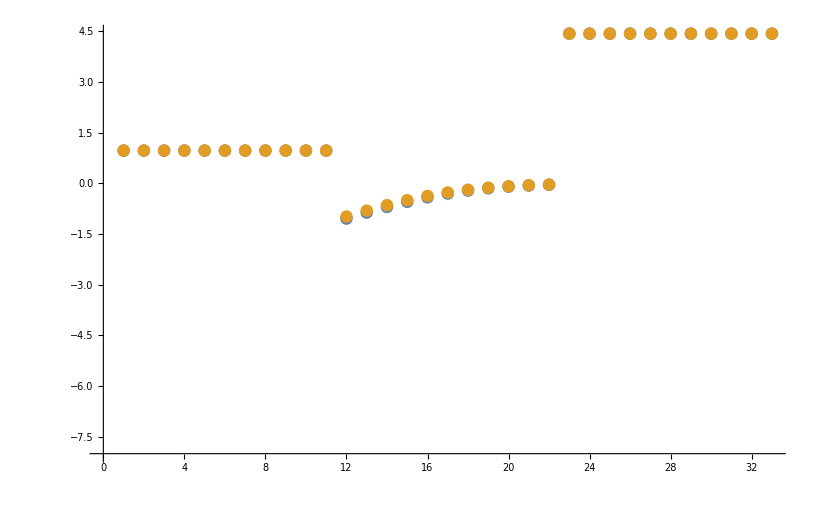

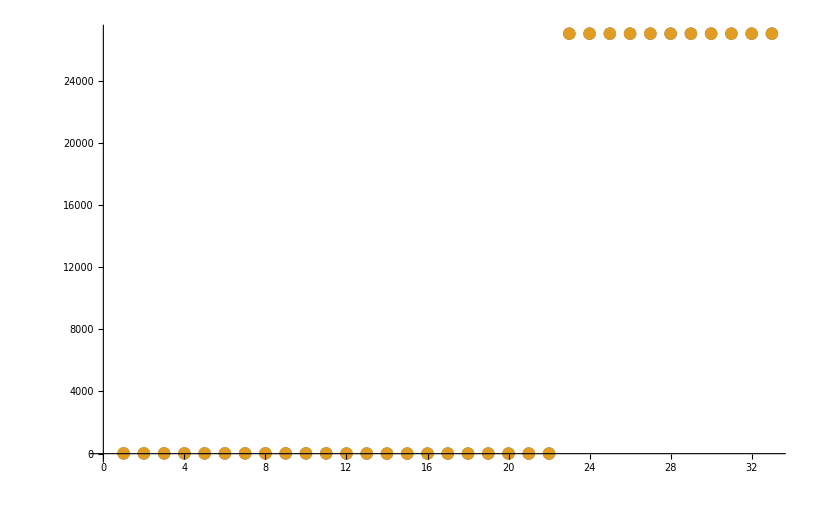

```mathematica
datasetI=40;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

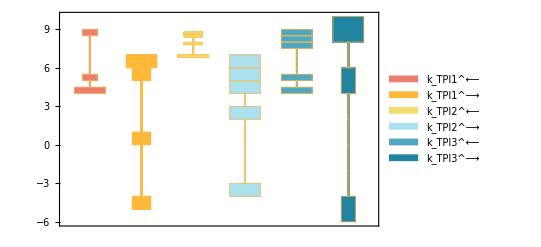

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

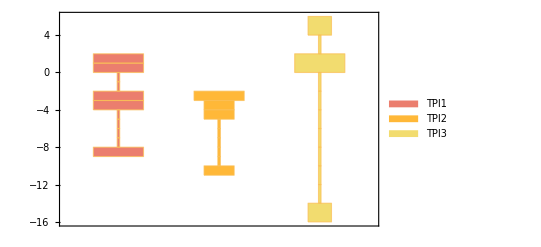

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

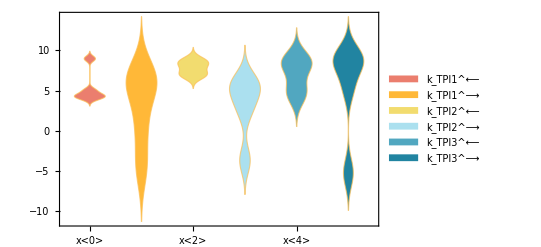

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1
assumedSaturatingConc=1
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[1,2]]]
```

TPI_total_Global→1

1

{k_TPI1^⟵→31314.5,k_TPI1^⟶→3.76306×10^7,k_TPI2^⟵→9.2187×10^6,k_TPI2^⟶→43438.3,k_TPI3^⟵→4.46269×10^8,k_TPI3^⟶→7.36902×10^8}

```mathematica
backCalculateKmsLocal[rxn, kmList, relativeRateForward, relativeRateReverse, metSatForSub, metSatRevSub,paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

g3p^c

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{g3p^c→(k_TPI1^⟵ k_TPI2^⟶+k_TPI1^⟵ k_TPI3^⟵+k_TPI2^⟶ k_TPI3^⟶)/(2. k_TPI1^⟵ k_TPI2^⟶+k_TPI1^⟶ k_TPI2^⟶+2. k_TPI1^⟵ k_TPI3^⟵+k_TPI1^⟶ k_TPI3^⟵+k_TPI1^⟶ k_TPI3^⟶+2. k_TPI2^⟶ k_TPI3^⟶)}}

{}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{g3p^c→0.00103068}}

data value | predicted value | error in %
0.00103 | 0.00103068 | 0.0658914

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse, metSatForSub, metSatRevSub,paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

data value | predicted value | error in %
0.00103 | 0.00103068 | 0.0658914

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
27025.3 | 27025.3 | 3.22804×10^-10

```mathematica
backCalculateRatios[haldaneRatiosList, KeqList[[1]][[3]],  paramFitSub]//TableForm
```

data value | predicted value | error in %
9.35 | 9.35 | 1.9514×10^-7

```mathematica
dhapCoSubKm = {};
dhapCoSubKcat = {dhap^c->1};
relRatedhap=Values@FilterRules[fileListSub,inputPath<>"/relRateRev_dhap.txt"];
absRateRev=Values@FilterRules[fileListSub,inputPath<>"/absRateRev.txt"];
```

```mathematica
backCalulateKmSimple[relRate_,paramFitSub_,coSub_,substrate_]:=Block[{kmPredicted},

  kmPredicted = Solve[(relRate/.paramFitSub/. coSub)==0.5, substrate];
	kmPredicted = Flatten[Values @ kmPredicted];
  kmPredicted = If[Length[kmPredicted] > 1,
					Flatten[Select[kmPredicted, Head[#] === Real && #> 0  &]][[1]],
					kmPredicted
				];
Return[kmPredicted]
];
```

```mathematica
absRateRev
```

{(dhap^c TPI_total_Global k_TPI1^⟵ k_TPI2^⟵ k_TPI3^⟵)/(k_TPI1^⟵ (k_TPI2^⟶+k_TPI3^⟵)+k_TPI2^⟶ k_TPI3^⟶+dhap^c k_TPI2^⟵ (k_TPI1^⟵+k_TPI3^⟵+k_TPI3^⟶))}

```mathematica
relRatedhap
```

{(dhap^c (k_TPI1^⟵ (k_TPI2^⟵+k_TPI2^⟶+k_TPI3^⟵)+k_TPI2^⟶ k_TPI3^⟶+k_TPI2^⟵ (k_TPI3^⟵+k_TPI3^⟶)))/(k_TPI1^⟵ (k_TPI2^⟶+k_TPI3^⟵)+k_TPI2^⟶ k_TPI3^⟶+dhap^c k_TPI2^⟵ (k_TPI1^⟵+k_TPI3^⟵+k_TPI3^⟶))}

#### Export rate back calculated parameter error distribution

```mathematica
flagFitType
```

log_ssd

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
nRateSets=100;
rateConstList=Import[outputPath<>"/treated_data/rateconst_TPI_"<>fitLabel<>"_"<>flagFitType<>".csv", "TSV"];

predictedParamsErrorList=Table[

(*paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[rateSetI,2]]];*)
paramFitSub=Thread[rateConstsSub[[All,1]]->rateConstList[[rateSetI,2;;]]];

{rateConstList[[rateSetI,1]],
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse, metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName][[2,3]],
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc][[2,3]],
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]],  paramFitSub][[2,3]]}//Flatten,

{rateSetI, 1, nRateSets}];

predictedParamsErrorList=Insert[predictedParamsErrorList,{"ssd","Km_g3p","kcat_f","Keq"} , 1];
predictedParamsErrorList=Insert[predictedParamsErrorList,{0,kmList[[1]][[3]],kcatList[[1]][[3]], KeqList[[1]][[3]]}  ,2];
Export[outputPath<>"/treated_data/predicted_params_error_distribution_"<>fitLabel<>"_"<>flagFitType<>".csv",predictedParamsErrorList,"CSV"];


predictedParamsList=Table[

(*paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[rateSetI,2]]];*)
paramFitSub=Thread[rateConstsSub[[All,1]]->rateConstList[[rateSetI,2;;]]];

{rateConstList[[rateSetI,1]],
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse, metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName][[2,2]],
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc][[2,2]],
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]],  paramFitSub][[2,2]],
backCalulateKmSimple[relRatedhap,paramFitSub,dhapCoSubKm,dhap^c],
 absRateRev /. paramFitSub /. dhapCoSubKcat /. enzymeSub}//Flatten,

{rateSetI, 1, nRateSets}];

predictedParamsList=Insert[predictedParamsList,{"ssd","Km_g3p","kcat_f","Keq","Km_dhap","kcat_r"} , 1];
predictedParamsList=Insert[predictedParamsList,{0,kmList[[1]][[3]],kcatList[[1]][[3]], KeqList[[1]][[3]], 1, 1}  ,2];
Export[outputPath<>"/treated_data/predicted_params_distribution_predRevParams_"<>fitLabel<>"_"<>flagFitType<>".csv",predictedParamsList,"CSV"];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

```mathematica
backCalulateKmSimple[relRatedhap,paramFitSub,dhapCoSubKm,dhap^c]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{0.268099}

```mathematica
absRateRev
```

{(dhap^c TPI_total_Global k_TPI1^⟵ k_TPI2^⟵ k_TPI3^⟵)/(k_TPI1^⟵ (k_TPI2^⟶+k_TPI3^⟵)+k_TPI2^⟶ k_TPI3^⟶+dhap^c k_TPI2^⟵ (k_TPI1^⟵+k_TPI3^⟵+k_TPI3^⟶))}

```mathematica
absRateRev /. paramFitSub /. dhapCoSubKcat /. enzymeSub
```

{16.5559}

#### Export rate back calculated parameter distribution

```mathematica
nRateSets=100;
predictedParamsList=Table[

paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[rateSetI,2]]];
{filteredDataList[[rateSetI,1]],
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, rxnName][[2,2]],
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc][[2,2]],
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]],  paramFitSub][[2,2]]}//Flatten,

{rateSetI, 1, nRateSets}];

predictedParamsList=Insert[predictedParamsList,{"ssd","Km_g3p","kcat_f","Keq"} , 1];
predictedParamsList=Insert[predictedParamsList,{"Null",kmList[[1]][[3]],kcatList[[1]][[3]], KeqList[[1]][[3]]}  ,2];
Export[outputPath<>"/treated_data/predicted_params_distribution.csv",predictedParamsList,"CSV"];
```